-Graphics-

# Statistical Distributions and Model Analysis

## Statistical Distributions

-Graphics3D-

"Outline" |

### Webinar Part 1

Distribution Properties

Simulation of Distributions

Derived Distributions

Hypothesis Tests

Fitting Data to Distributions

Method of Moments Estimation

Bootstrapping & Confidence Estimation

### Webinar Part 2

Linear Model Fit

Nonlinear Model Fit

Fitting Theoretical Models

### Webinar Part 3

Generalized Linear Models

Piecewise Models

## Learning Objectives

### Statistical Distributions and Properties

This section is an overview of the distribution-related functions in the Wolfram Language™ for the following:

Different types of distributions

Properties of distributions

Simulation of distributions

### Fitting Data to Distributions

This section deals with various techniques of fitting data to distributions:

Data fitting to known parametric distributions

Fitting data to nonparametric distributions

Method of moments estimation

Bootstrapping for nonparametric distributions

-Graphics-

## Introduction to Distributions

The collection of Parametric Statistical Distributions in the Wolfram Language has been selected in order to provide complete modeling frameworks for a variety of areas. The result is the most extensive collection of continuous and discrete parametric distributions ever assembled, which includes univariate, multivariate and matrix distributions. Similarly, the Wolfram Language has Nonparametric Statistical Distributions (distributions that can be directly constructed from data), Derived Statistical Distributions (distributions that can be constructed from other distributions).

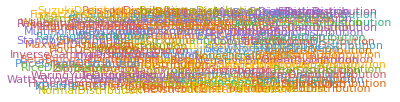

## Distribution Properties: Probability

#### Definition

The Probability function in the Wolfram Language gives the probability of an event, given that it follows the mentioned probability distribution. It is defined for both univariate and multivariate cases.

| "Univariate" | "Multivariate"
"Discrete" | ∑_(ξ=-∞)^∞ Boole[pred] f[ξ] | ∑_(ξ_1=-∞)^∞ ∑_(ξ_n=-∞)^∞ Boole[pred] f[ξ_1,…,ξ_n]
"Continuous" | ∫_(-∞)^∞ Boole[pred] f[ξ]ⅆξ | ∫_(-∞)^∞ ∫_(-∞)^∞ Boole[pred] f[ξ_1,…,ξ_n]ⅆ ξ_nⅆ ξ_1

#### Examples

Discrete univariate probabilities:

```mathematica
Probability[x≥1,x\[Distributed]BinomialDistribution[n,p]]
```

Nonlinear conditions:

```mathematica
Probability[(x-3)^2≥x,x\[Distributed]ZipfDistribution[ρ]]
```

Logical combinations:

```mathematica
Probability[k^2>10||k<2,k\[Distributed]PoissonDistribution[λ]]
```

Multivariate probabilities:

```mathematica
Probability[X≤1/2&&Y≤1,{X,Y}\[Distributed]DirichletDistribution[{1,2,3}]]
```

Conditional probabilities:

```mathematica
Probability[x^2>1\[Conditioned]x>1/2,x\[Distributed]LaplaceDistribution[0,1/2]]
```

Nonlinear logical combinations:

```mathematica
Probability[x^2+y^2<1/4∧x+y<6/7,{x,y}\[Distributed]DirichletDistribution[{2,3,4}]]
```

## Distribution Properties: Expectation

#### Definition

The Expectation function in the Wolfram Language gives the expectation of the expression, given that it follows the mentioned probability distribution. It is defined for both univariate and multivariate cases.

| "Univariate" | "Multivariate"
"Discrete" | ∑_(ξ=-∞)^∞ g[ξ] f[ξ] | ∑_(ξ_1=-∞)^∞ ∑_(ξ_n=-∞)^∞ g[ξ_1,…,ξ_n] f[ξ_1,…,ξ_n]
"Continuous" | ∫_(-∞)^∞ g[ξ] f[ξ]ⅆξ | ∫_(-∞)^∞ ∫_(-∞)^∞ g[ξ_1,…,ξ_n] f[ξ_1,…,ξ_n]ⅆ ξ_nⅆ ξ_1

#### Examples

Polynomial expectation:

```mathematica
Expectation[2x^4+3,x\[Distributed]NormalDistribution[]]
```

Expectation of an arbitrary expression:

```mathematica
Expectation[E^(-x)+3x,x\[Distributed]ChiSquareDistribution[ν]]
```

Conditional expectation:

```mathematica
Expectation[x^2+1\[Conditioned]x>1/2,x\[Distributed]LaplaceDistribution[0,1/2]]
```

Expectation with Quantity:

```mathematica
Expectation[Quantity[v,"Meters"/"Seconds"] Quantity[t,"Minutes"],{v\[Distributed]MaxwellDistribution[σ],t\[Distributed]GammaDistribution[a,b]}]
```

## Distribution Properties

### Distribution Functions

#### Definition

In this section, you will see how to obtain the probability density function (PDF) (or probability mass function in discrete cases), cumulative density function (CDF), survival function SurvivalFunction (SF) and HazardFunction (HF) and visualize them using different built-in visualization techniques. For the different classes of distributions (depending on discrete versus continuous or univariate versus multivariate), the visualization function used will vary. First, look at the definitions of these functions:

1234

#### Examples

Univariate continuous:

```mathematica
Manipulate[Plot[Table[func[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis],{{func,PDF,"ProbabilityFunction"},{PDF,CDF,SurvivalFunction,HazardFunction}}]
```

Univariate discrete:

```mathematica
Manipulate[DiscretePlot[Table[func[GeometricDistribution[p],k],{p,{0.1,0.2,0.5}}]//Evaluate,{k,0,14},ExtentSize->Right],{{func,PDF,"ProbabilityFunction"},{PDF,CDF,SurvivalFunction,HazardFunction}}]
```

Multivariate continuous:

```mathematica
Manipulate[Plot3D[func[BinormalDistribution[1/2],{x,y}],{x,-1,3},{y,-1,3},PlotRange->All,MaxRecursion->0],{{func,PDF,"ProbabilityFunction"},{PDF,CDF,SurvivalFunction,HazardFunction}}]
```

Multivariate discrete:

```mathematica
Manipulate[DiscretePlot3D[func[MultinomialDistribution[10,{1/3,2/3}],{x,y}],{x,-1,7},{y,-1,7},ExtentSize->Right],{{func,PDF,"ProbabilityFunction"},{PDF,CDF,SurvivalFunction,HazardFunction}}]
```

## Distribution Properties

### Moments

#### Definition

In the Wolfram Language, you can obtain the raw moment, Moment; the moment about the mean, CentralMoment; the factorial moment, FactorialMoment; and the cumulant, Cumulant.

123

#### Examples

Compute the second Moment μ_2 of a univariate distribution:

```mathematica
Moment[NormalDistribution[μ,σ],2]
```

The second and third instances of CentralMoment as measures of dispersion and skewness:

```mathematica
CentralMoment[NormalDistribution[μ,σ],2]
```

Zero-skewed, positively skewed and negatively skewed distributions:

```mathematica
{CentralMoment[NormalDistribution[1,2],3], CentralMoment[ChiSquareDistribution[2],3],CentralMoment[GumbelDistribution[1,2],3]}//N
```

Tabulate moments up to order 5 for the GammaDistribution:

```mathematica
MomentTabView[GammaDistribution[α,β],5]
```

1234

### Moment-Generating Functions

Similarly to the moments, the moment-generating function corresponding to each of the preceding four moments can be obtained.

Moment-generating functions for the GammaDistribution:

```mathematica
Manipulate[f[GammaDistribution[α,β],t],{{f,f,"f[t]"},{MomentGeneratingFunction->"MGF",CentralMomentGeneratingFunction->"CentralMGF",FactorialMomentGeneratingFunction->"FactorialMGF",CumulantGeneratingFunction->"CumulantGF"}}]
```

## Simulation of Distributions

RandomVariate simulates both continuous and discrete distributions. Note the use of different functions to visualize data obtained from simulating different classes of distributions.

Univariate continuous:

```mathematica
data=RandomVariate[NormalDistribution[1,3],10^4];
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,3],x],{x,Min[data],Max[data]},PlotStyle->Thick]]
```

Multivariate discrete:

```mathematica
data=RandomVariate[MultivariatePoissonDistribution[1,{2,3}],10^4];
{Histogram3D[data,20,"Probability",PlotRange->{{0,10},{0,10},All}],
DiscretePlot3D[PDF[MultivariatePoissonDistribution[1,{2,3}],{x,y}],{x,Min[data],Max[data]},{y,Min[data],Max[data]},PlotRange->All,ExtentSize->Full]}
```

Mixture distributions:

```mathematica
𝒟 =MixtureDistribution[{1,3}, {NormalDistribution[0,1],NormalDistribution[6,2]}];
data = RandomVariate[𝒟,10^5];
Show[Histogram[data,50,"PDF"],Plot[PDF[𝒟,x],{x,Min[data],Max[data]}]]
```

## Derived Distributions

Derived distributions are modifications to existing distributions. There is a variety of ways in which you can arrive at modified distributions, including functions of random variables, weighted mixtures of distributions, truncated or censored distributions, marginals from higher-dimensional distributions, or joining marginals to a dependency kernel, as in copulas. Derived distributions behave just like any other distribution in the Wolfram Language. You can compute several dozen properties, including distribution functions or probabilities of events, or generate random variates from them.

### Transformed Distribution

#### Examples

Linear transformation:

```mathematica
TransformedDistribution[2 u+b,u\[Distributed]NormalDistribution[μ,σ]]
```

Nonlinear transformations:

```mathematica
TransformedDistribution[Exp[u],u\[Distributed]NormalDistribution[μ,σ]]
```

```mathematica
𝒟=TransformedDistribution[u^2,u\[Distributed]BetaDistribution[4,3]]
```

You can extract all information from a TransformedDistribution, like any other distribution:

```mathematica
Plot[PDF[𝒟,x],{x,0,1},Filling->Axis]
```

#### Problems

An example from the book Dimitri P. Bertsekas and John N. Tsitsiklis:
Two archers shoot at a target. The distance of each shot from the center of the target is uniformly distributed from 0 to 1 inches, independent of the other shot. Find the probability that the losing shot is more than 0.5 inches away from the target:

```mathematica
LosingShotD=TransformedDistribution[Max[x,y],{x,y}\[Distributed]UniformDistribution[{{Quantity[0, "Inches"],Quantity[1, "Inches"]},{Quantity[0, "Inches"],Quantity[1, "Inches"]}}]];
```

```mathematica
Probability[z>Quantity[0.5,"Inches"],z\[Distributed]LosingShotD]
```

0.75

#### How To Plot

QuantityDistribution[TransformedDistribution[Max[x1,x2],{x1,x2}\[Distributed]UniformDistribution[{{0,1},{0,1}}]], in]

{{0.,1.},{0.1,0.99},{0.2,0.96},{0.3,0.91},{0.4,0.84},{0.5,0.75},{0.6,0.64},{0.7,0.51},{0.8,0.36},{0.9,0.19},{1.,0}}

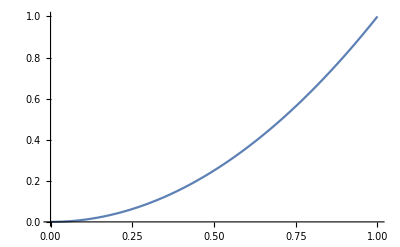

```mathematica
LosingShotD
Table[{cutoff, Probability[z>Quantity[cutoff,"Inches"],z\[Distributed]LosingShotD]},{cutoff, 0, 1, 0.1}]
Plot[CDF[LosingShotD,Quantity[w,"Inches"]]//Evaluate,{w,0,1}]
```

### Order Distribution

This represents the k^th-order statistics distribution for n observations from a distribution.

#### Examples

Find the distribution of the maximum of a sample of a continuous distribution:

```mathematica
𝒟=OrderDistribution[{NormalDistribution[3,2],n},n];
```

Find the probability density function:

```mathematica
PDF[𝒟,x]
```

Plot the PDF for different sample sizes:

```mathematica
Plot[Table[Legended[PDF[𝒟,x],Row[{"n"," = ",n}]],{n,{5,10,20}}]//Evaluate,{x,1,10},Filling->Axis]
```

### Truncated Distribution

This represents a distribution obtained by truncating the values of a given distribution between the given limits.

#### Examples

Truncate a Cauchy distribution from -∞ to 1.0:

```mathematica
𝒹=CauchyDistribution[0,1]; 𝒟=TruncatedDistribution[{-∞,1.0},𝒹];
```

Plot the truncated distribution:

```mathematica
Plot[{Legended[PDF[𝒹,x],"𝒹"],Legended[PDF[𝒟,x],"𝒟"]},{x,-5,5},Filling->Axis]
```

## Hypothesis Tests

Hypothesis tests can be used to answer questions such as how good the fit is between data and a particular distribution, whether these distributions have the same mean or median, and whether these datasets have the same variability. The Wolfram Language provides high-level functions for these types of questions and will automatically select the tests applicable for the data and distributions given. The high-level functions typically run more than one test and are able to produce full reports, but there are also specific named hypothesis tests. These named hypothesis tests give more direct control over settings and performance for specific tests.

### DistributionFitTest

This performs a goodness-of-fit hypothesis test with null hypothesis H_0 that data was drawn from a population with distribution dist and alternative hypothesis H_a that it was not. By default, a probability value, also known as a p-value, is returned. A small p-value suggests that it is unlikely that the data came from dist. DistributionFitTest applies the most powerful test to given data and dist for a general alternative hypothesis:

```mathematica
data=RandomVariate[NormalDistribution[],2500];
```

```mathematica
GraphicsRow[{ProbabilityPlot[data,NormalDistribution[],PlotLabel->"ProbabilityPlot"],
QuantilePlot[data,NormalDistribution[],PlotLabel-> "QuantilePlot"]},ImageSize->1000]
```

```mathematica
fittest=DistributionFitTest[data,Automatic,"HypothesisTestData"];
```

```mathematica
fittest["TestDataTable",All]
```

```mathematica
Column[{Style[fittest["ShortTestConclusion"],"Text"],Style[fittest["TestConclusion"],"Text"]},Frame->True]
```

### LocationTest

LocationTest performs a hypothesis test on data with null hypothesis H_0 that the true population has a location parameter is some value μ=μ_0, and alternative hypothesis H_a that μ≠μ_0. By default, a probability value or p-value is returned. A small p-value suggests that it is unlikely that H_0 is true.

Test if the means of two populations differ by 2:

```mathematica
BlockRandom[SeedRandom[1];
data1=RandomVariate[NormalDistribution[1.85,1],1000];
data2=RandomVariate[NormalDistribution[0,1],1000];]
```

```mathematica
BoxWhiskerChart[{data1,data2},"Notched",ChartStyle->"SolarColors"]
```

Mean difference μ_1-μ_2:

```mathematica
Mean[data1]-Mean[data2]
```

At the 0.05 level, the mean difference μ_1-μ_2 is significantly different from 2:

```mathematica
LocationTest[{data1,data2},2]
```

Similarly, the LocationEquivalenceTest compares the means or medians of two or more datasets.

### VarianceTest

VarianceTest tests the null hypothesis H_0 against the alternative hypothesis H_a:

where σ_i^2 is the population variance for data_i. By default, a probability value or p-value is returned. A small p-value suggests that it is unlikely that H_0 is true:

```mathematica
SeedRandom[1];data1=RandomVariate[NormalDistribution[0,1],100];
data2=RandomVariate[NormalDistribution[0,1],100];
data3=RandomVariate[NormalDistribution[0,3],100];
```

```mathematica
BoxWhiskerChart[{data1,data2,data3},"Notched",ChartStyle->"SolarColors"]
```

The first two populations have similar variances:

```mathematica
VarianceTest[{data1,data2},Automatic,"TestDataTable"]
```

The third population differs in variance from the first:

```mathematica
VarianceTest[{data1,data3},Automatic,"TestDataTable"]
```

## Fitting Data to Known Distributions

For estimating if particular data follows a distribution, you can use DistributionFitTest.

The lottery.txt file contains information on the Maryland Pick 3 lottery. The winning numbers are returned as three-digit numbers from 000 to 999. If the lottery is fair, you would expect the winning numbers to come from a uniform distribution defined on the interval {0,999}. That can be checked visually and quantitatively.

### Visualizations

Apply Import to the data:

```mathematica
lotDat=Import[FileNameJoin[{NotebookDirectory[],"lottery.txt"}],"List"];
```

Visualize the data by plotting a Histogram, along with DistributionChart and BoxWhiskerChart. Finally, QuantilePlot will help compare the data to a UniformDistribution:

```mathematica
GraphicsRow[{Histogram[lotDat,10,PlotLabel-> "Histogram"],
DistributionChart[lotDat,PlotLabel-> "DistributionChart"],
BoxWhiskerChart[lotDat,PlotLabel-> "BoxWhiskerChart"],
QuantilePlot[lotDat,UniformDistribution[{0,999}],PlotLabel-> "QuantilePlot"]},ImageSize->1000]
```

### Quantitative Fitting

Now you can do a quantitative test. DistributionFitTest can be used to determine if your assumptions about the fairness of the lottery are reasonable:

```mathematica
ftTst= DistributionFitTest[lotDat,UniformDistribution[{0,999}],"HypothesisTestData"]
```

Here are the properties available from the test:

```mathematica
ftTst["Properties"]
```

The tests that are relevant for this particular case:

```mathematica
ftTst["TestDataTable",All]
```

```mathematica
Column[{Style[ftTst["ShortTestConclusion"],"Text"],Style[ftTst["TestConclusion"],"Text"]},Frame->True]
```

## Fitting Data to Distributions

In the case that you have no prior knowledge of the distribution to fit the data points, there are two alternatives:
 	i)  Use a nonparametric distribution estimator.
 	ii) Use FindDistribution to select parametric distribution based on parameter fit.

In the US, the largest wind power center is situated at Alta Wind Energy Center in California. Visualize the location and then analyze the wind data obtained there, using the built-in functions in the Wolfram Language:

```mathematica
GeoGraphics[GeoMarker[GeoPosition[{35.021111,-118.320556}]],GeoRange->Quantity[200, "Kilometers"]]
```

-Graphics-

In this example, you will try to fit wind speed data to a parametric as well as a nonparametric distribution and find the probability that the wind speed is greater than the cutoff wind speed required to generate power.

### Getting the Data via WeatherData

In this example, information from WeatherData is used to investigate the feasibility of using wind to generate electricity. First, obtain the data, then clean it to remove the missing values:

```mathematica
(*wndData=TimeSeries[WeatherData[GeoPosition[{35.021111,-118.320556}], "MeanWindSpeed",{{2000,1,1},Date[],"Day"}],MissingDataMethod->Automatic];*)
dataclean=QuantityMagnitude@wndData["Values"];
```

```mathematica
DateListPlot[wndData]
```

Visualize the data in histograms for the PDF and CDF:

```mathematica
GraphicsRow[{histplotpdf,histplotcdf}={Histogram[QuantityMagnitude@wndData,45,"PDF",PlotLabel->"PDF"],Histogram[QuantityMagnitude@wndData,45,"CDF",PlotLabel->"CDF"]},ImageSize-> Large]
```

## Fitting Data with No Prior Knowledge of the Distribution

### Fitting to a Nonparametric Distribution

Since wind speed can be assumed to vary continuously, estimate a distribution for observations using the SmoothKernelDistribution function. Find an estimated distribution and visualize the results. This assumes the data comes from a continuous distribution:

```mathematica
Subscript[𝒟, e]=SmoothKernelDistribution[dataclean]
```

Visualize how good the fit is and conclude with a quantitative estimate:

```mathematica
GraphicsRow[{Show[{
histplotpdf,
estplot= Plot[PDF[Subscript[𝒟, e],x],{x,0,90},PlotStyle->Thick]
}],Show[{
histplotcdf,
estplot= Plot[CDF[Subscript[𝒟, e],x],{x,0,90},PlotStyle->Thick]}
]},ImageSize-> Large]
```

```mathematica
tstData=DistributionFitTest[dataclean,Subscript[𝒟, e],"HypothesisTestData"];
tstData["TestDataTable", All]
```

```mathematica
Column[{Style[tstData["ShortTestConclusion"],"Text"],Style[tstData["TestConclusion"],"Text"]},Frame->True]
```

### Fitting to Parametric Distributions

An alternate approach would be to fit the data to known parametric distributions using FindDistribution:

```mathematica
Subscript[𝒟, p]=FindDistribution[dataclean]
```

```mathematica
tstData=DistributionFitTest[dataclean,Subscript[𝒟, p],"HypothesisTestData"];
tstData["TestDataTable", All]
```

Visualize how good the fit is:

```mathematica
GraphicsRow[{Show[{
histplotpdf,
estplot= Plot[PDF[Subscript[𝒟, p],x],{x,0,90},PlotStyle->Thick]
}],Show[{
histplotcdf,
estplot= Plot[CDF[Subscript[𝒟, p],x],{x,0,90},PlotStyle->Thick]}
]},ImageSize-> Large]
```

The cutoff wind speed for wind generation is approximately 12 km/h. You can find out what probability each of these models predicts for successful wind power generation:

```mathematica
Probability[x>12.0,x\[Distributed] Subscript[𝒟, p]]
```

```mathematica
Probability[x>12.0,x\[Distributed] Subscript[𝒟, e]]
```

## Method of Moments Estimation

In this example, the use of method of moments as an estimation criterion to fit data to a known parametric distribution (or a mixture of parametric distributions) is considered.

The Wolfram Language has built-in curated data. Bring the data of the Old Faithful geyser into the Wolfram Language and check the dimensions:

```mathematica
ofData=ExampleData[{"Statistics","OldFaithful"}];
```

```mathematica
Dimensions[ofData]
```

Reorient the data into columns and assign names:

```mathematica
{dur,wait}= Transpose[ofData];
```

Look for patterns in the data. The scales are very different, as can be seen from the values on the horizontal axes:

```mathematica
GraphicsRow[{Histogram[dur,12,"PDF",ChartElementFunction-> "GlassRectangle",PlotLabel-> Style["Duration","Text"]],Histogram[wait,12,"PDF",ChartElementFunction-> "GlassRectangle",PlotLabel-> Style["Waiting Time","Text"]]},ImageSize-> Large]
```

Perform a linear rescaling and translation of the data:

```mathematica
sclData1=With[{dat1=MinMax[dur],dat2=MinMax[wait]},Rescale[#,dat1,dat2]&/@dur];
```

Using PairedHistogram lets you see that the patterns are very similar for the two lists:

```mathematica
PairedHistogram[sclData1,wait,12,"PDF",ChartElementFunction-> "GlassRectangle",ChartLabels-> {Style["Scaled Duration","Text"],Style["Waiting Time","Text"]}]
```

### Fitting Waiting Times Using EstimatedDistribution

```mathematica
Clear[p,p1]
```

```mathematica
asc=AssociationMap[EstimatedDistribution[wait,MixtureDistribution[{p,1-p},{NormalDistribution[m1,s1],NormalDistribution[m2,s2]}],ParameterEstimator->#]&,{"MaximumLikelihood","MethodOfMoments"}]
```

```mathematica
Show[{Histogram[wait,25,"PDF"],Plot[PDF[asc[[1]],x],{x,34,100},PlotStyle-> Orange],Plot[PDF[asc[[2]],x],{x,34,100}]}]
```

### Fitting Duration of the Eruption Using EstimatedDistribution

```mathematica
asc2=AssociationMap[ EstimatedDistribution[dur,MixtureDistribution[{p1,1-p1},{NormalDistribution[m1,s1],NormalDistribution[m2,s2]}],ParameterEstimator->#]&,{"MaximumLikelihood","MethodOfMoments"}]
```

```mathematica
Show[{Histogram[dur,25,"PDF"],Plot[PDF[asc2[[1]],x],{x,0,7},PlotStyle-> Orange],Plot[PDF[asc2[[2]],x],{x,0,7}]}]
```

## Bootstrapping and Confidence Estimate

While fitting to a distribution, it is often useful to obtain and visualize a confidence band. In this example, the PDF of a dataset will be obtained, along with the confidence band, by bootstrapping (randomly selecting some examples) from the dataset.

Create a confidence band for the PDF of snowfall accumulations in Buffalo, New York:

```mathematica
ExampleData[{"Statistics","BuffaloSnow"},"Description"]
```

```mathematica
datasnow=QuantityArray[ExampleData[{"Statistics","BuffaloSnow"}]//N,"Inches"];
```

```mathematica
Length[datasnow]
```

```mathematica
𝒟=SmoothKernelDistribution[datasnow];
```

Create a set of 250 datasets by random sampling from the data and allowing repetitions in a dataset:

```mathematica
bSamp=RandomChoice[Normal[datasnow],{250,Length[datasnow]}];
```

Smooth over each bootstrapped sample and obtain the confidence estimates:

```mathematica
Subscript[𝒟, B]=SmoothKernelDistribution[#]&/@bSamp;
```

Finally, obtain the confidence band from the bootstrapped examples:

```mathematica
rng=Range[10.,150];
pdf=Table[PDF[i,Quantity[rng,"Inches"]],{i,Subscript[𝒟, B]}];
High=Table[Quantile[i,.975],{i,Transpose[pdf]}];
Low = Table[Quantile[i,.025],{i,Transpose[pdf]}];
```

Visualize the estimate of the PDF with the 95% confidence band:

```mathematica
Show[Plot[PDF[𝒟,Quantity[x,"Inches"]],{x,0,150},PlotRange->All,AxesLabel->{"in"}],ListLinePlot[{Transpose[{rng,High}],Transpose[{rng,Low}]},PlotStyle->{{Dashed,Gray}},Filling->{1->{2}}]]
```

## Glossary

AssociationMap | AxesLabel | AxesOrigin | Axis | BinomialDistribution
BinormalDistribution | BoundaryStyle | BoxWhiskerChart | Cases | CDF
ChartElementFunction | ChiSquareDistribution | Column | Dashed | Date
Directive | DirichletDistribution | DiscretePlot | DiscretePlot3D | DistributionChart
DistributionFitTest | EstimatedDistribution | Evaluate | ExampleData | ExtentSize
FileNameJoin | Filling | FillingStyle | FindDistribution | FontFamily
Frame | GammaDistribution | GeoGraphics | GeoMarker | GeometricDistribution
GeoRange | GraphicsRow | HazardFunction | Histogram | ImageSize
Import | Labeled | LaplaceDistribution | Large | Length
ListLinePlot | Manipulate | Max | MaximumLikelihood | MaxRecursion
MethodOfMoments | Min | MixtureDistribution | MultivariatePoissonDistribution | N
Normal | NormalDistribution | NotebookDirectory | NumericQ | PairedHistogram
ParameterEstimator | PDF | Plot | Plot3D | PlotLabel
PlotRange | PlotStyle | PoissonDistribution | Probability | ProductDistribution
Quantile | QuantilePlot | QuantityArray | QuantityMagnitude | RandomChoice
RandomVariate | RegionPlot | Rescale | Row | Show
SmoothKernelDistribution | Sqrt | Style | SurvivalFunction | Table
Thick | TimeSeries | TraditionalForm | Transpose | UniformDistribution
WeatherData | With | ZipfDistribution |  |

## Review Exercises

Provided separately

## Initialize Slide

```mathematica
CellDisplay[expr_]:=CellPrint[ExpressionCell[expr,"Output",Background->None,ShowCellLabel->False,CellFrame->False,CellMargins->{{100,100},{40,0}},"Output",GeneratedCell->False]];
MomentGrid[list_,type_]:=
Grid[Transpose@{list},Alignment->{Left,Automatic},Background->{None,{{Lighter[Blend[Switch[type,Moment,{Blue,Green},CentralMoment,{Red,Orange},FactorialMoment,{Magenta,Cyan},Cumulant,{Purple,Red}]],.8],White}}},Dividers->{None,{Darker[Gray,.6],{False},Darker[Gray,.6]}},ItemSize->30];
MomentTabView[dist_,n_Integer?Positive]:=
CellDisplay@TabView[{"Moment"->MomentGrid[Table[Moment[dist,k],{k,n}],Moment],"CentralMoment"->MomentGrid[Table[CentralMoment[dist,k],{k,n}],CentralMoment],"FactorialMoment"->MomentGrid[Table[FactorialMoment[dist,k],{k,n}],FactorialMoment],"Cumulant"->MomentGrid[Table[Cumulant[dist,k],{k,n}],Cumulant]}];
```

```mathematica
(*wndData=TimeSeries[WeatherData[GeoPosition[{35.021111,-118.320556}], "MeanWindSpeed",{{2000,1,1},Date[],"Day"}],MissingDataMethod->Automatic];*)
```

```mathematica
wndData=TimeSeries[…]
```

TimeSeries[…]

```mathematica
ofData={{3.6,79},{1.8,54},{3.333,74},{2.283,62},{4.533,85},{2.883,55},{4.7,88},{3.6,85},{1.95,51},{4.35,85},{1.833,54},{3.917,84},{4.2,78},{1.75,47},{4.7,83},{2.167,52},{1.75,62},{4.8,84},{1.6,52},{4.25,79},{1.8,51},{1.75,47},{3.45,78},{3.067,69},{4.533,74},{3.6,83},{1.967,55},{4.083,76},{3.85,78},{4.433,79},{4.3,73},{4.467,77},{3.367,66},{4.033,80},{3.833,74},{2.017,52},{1.867,48},{4.833,80},{1.833,59},{4.783,90},{4.35,80},{1.883,58},{4.567,84},{1.75,58},{4.533,73},{3.317,83},{3.833,64},{2.1,53},{4.633,82},{2.,59},{4.8,75},{4.716,90},{1.833,54},{4.833,80},{1.733,54},{4.883,83},{3.717,71},{1.667,64},{4.567,77},{4.317,81},{2.233,59},{4.5,84},{1.75,48},{4.8,82},{1.817,60},{4.4,92},{4.167,78},{4.7,78},{2.067,65},{4.7,73},{4.033,82},{1.967,56},{4.5,79},{4.,71},{1.983,62},{5.067,76},{2.017,60},{4.567,78},{3.883,76},{3.6,83},{4.133,75},{4.333,82},{4.1,70},{2.633,65},{4.067,73},{4.933,88},{3.95,76},{4.517,80},{2.167,48},{4.,86},{2.2,60},{4.333,90},{1.867,50},{4.817,78},{1.833,63},{4.3,72},{4.667,84},{3.75,75},{1.867,51},{4.9,82},{2.483,62},{4.367,88},{2.1,49},{4.5,83},{4.05,81},{1.867,47},{4.7,84},{1.783,52},{4.85,86},{3.683,81},{4.733,75},{2.3,59},{4.9,89},{4.417,79},{1.7,59},{4.633,81},{2.317,50},{4.6,85},{1.817,59},{4.417,87},{2.617,53},{4.067,69},{4.25,77},{1.967,56},{4.6,88},{3.767,81},{1.917,45},{4.5,82},{2.267,55},{4.65,90},{1.867,45},{4.167,83},{2.8,56},{4.333,89},{1.833,46},{4.383,82},{1.883,51},{4.933,86},{2.033,53},{3.733,79},{4.233,81},{2.233,60},{4.533,82},{4.817,77},{4.333,76},{1.983,59},{4.633,80},{2.017,49},{5.1,96},{1.8,53},{5.033,77},{4.,77},{2.4,65},{4.6,81},{3.567,71},{4.,70},{4.5,81},{4.083,93},{1.8,53},{3.967,89},{2.2,45},{4.15,86},{2.,58},{3.833,78},{3.5,66},{4.583,76},{2.367,63},{5.,88},{1.933,52},{4.617,93},{1.917,49},{2.083,57},{4.583,77},{3.333,68},{4.167,81},{4.333,81},{4.5,73},{2.417,50},{4.,85},{4.167,74},{1.883,55},{4.583,77},{4.25,83},{3.767,83},{2.033,51},{4.433,78},{4.083,84},{1.833,46},{4.417,83},{2.183,55},{4.8,81},{1.833,57},{4.8,76},{4.1,84},{3.966,77},{4.233,81},{3.5,87},{4.366,77},{2.25,51},{4.667,78},{2.1,60},{4.35,82},{4.133,91},{1.867,53},{4.6,78},{1.783,46},{4.367,77},{3.85,84},{1.933,49},{4.5,83},{2.383,71},{4.7,80},{1.867,49},{3.833,75},{3.417,64},{4.233,76},{2.4,53},{4.8,94},{2.,55},{4.15,76},{1.867,50},{4.267,82},{1.75,54},{4.483,75},{4.,78},{4.117,79},{4.083,78},{4.267,78},{3.917,70},{4.55,79},{4.083,70},{2.417,54},{4.183,86},{2.217,50},{4.45,90},{1.883,54},{1.85,54},{4.283,77},{3.95,79},{2.333,64},{4.15,75},{2.35,47},{4.933,86},{2.9,63},{4.583,85},{3.833,82},{2.083,57},{4.367,82},{2.133,67},{4.35,74},{2.2,54},{4.45,83},{3.567,73},{4.5,73},{4.15,88},{3.817,80},{3.917,71},{4.45,83},{2.,56},{4.283,79},{4.767,78},{4.533,84},{1.85,58},{4.25,83},{1.983,43},{2.25,60},{4.75,75},{4.117,81},{2.15,46},{4.417,90},{1.817,46},{4.467,74}};
```

```mathematica
datas={126.4,82.4,78.1,51.1,90.9,76.2,104.5,87.4,110.5,25,69.3,53.5,39.8,63.6,46.7,72.9,79.7,83.6,80.7,60.3,79,74.4,49.6,54.7,71.8,49.1,103.9,51.6,82.4,83.6,77.8,79.3,89.6,85.5,58,120.7,110.5,65.4,39.9,40.1,88.7,71.4,83,55.9,89.9,84.8,105.2,113.7,124.7,114.5,115.6,102.4,101.4,89.8,71.5,70.9,98.3,55.5,66.1,78.4,120.5,97,110};
datasnow=QuantityArray[datas//N,"Inches"];
```